```mathematica
thetadata=Import[NotebookDirectory[]<>"100mev_theta_relation.csv"][[2;;]]
```

{{5.4748,0.23605},{1.56116,0.0929256},{8.47594,0.447761},{6.25677,1.82672},7226,{5.28576,0.136442},{2.9785,0.29751},{3.05402,0.342149},{10.6481,0.133359}}
 |  |  |  |

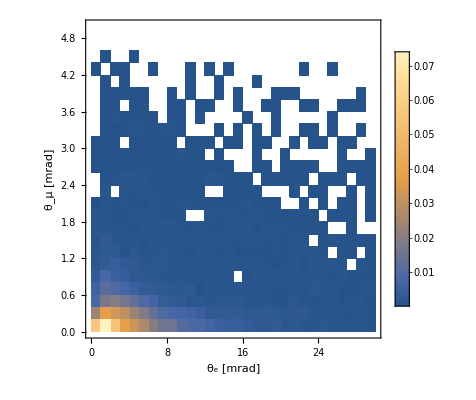

```mathematica
distribution=DensityHistogram[thetadata,Automatic,"Probability",PlotRange->{{0,30},{0,5}},ChartLegends->Automatic,BaseStyle->{FontSize->14,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{"θ_e [mrad]","θ_μ [mrad]"},LabelStyle->{Black},PlotRangePadding->None]
```

```mathematica
Eμ=150;
mμ=0.105;
me=5.11*10^-4;
```

```mathematica
tsolve=Solve[Cos[θe/1000]==(Eμ T + me T)/(√(Eμ^2-mμ^2)√(T(2me+T))),T]
```

{{T→-(1.97555×10^19 Cos[0.001 θe]^2)/(-1.93303×10^22+1.93302×10^22 Cos[0.001 θe]^2)}}

```mathematica
tanθμ=(√(T(2me+T))Sin[θe/1000])/(√(Eμ^2-mμ^2)-Cos[θe/1000] √(T(2me+T)))/.tsolve//Simplify
```

{-(1. √(Cos[0.001 θe]^2/((1.93303×10^22-1.93302×10^22 Cos[0.001 θe]^2)^2)) Sin[θe/1000])/(-7.59281×10^-18+1. √(Cos[0.001 θe]^2/((1.93303×10^22-1.93302×10^22 Cos[0.001 θe]^2)^2)) Cos[θe/1000])}

```mathematica
θμ[θe_]:=1000*ArcTan[tanθμ]
```

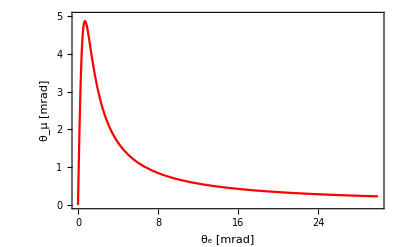

```mathematica
elastic=Plot[θμ[θe],{θe,0,30},PlotRange->{{0,30},{0,5}},BaseStyle->{FontSize->14,FontFamily->"Times"},Frame->True,FrameLabel->{"θ_e [mrad]","θ_μ [mrad]"},LabelStyle->{Black},PlotRangePadding->None,PlotStyle->{Red}]
```

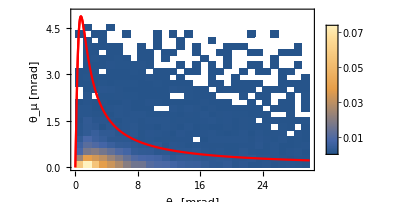

```mathematica
combine=Show[elastic,distribution,elastic,ImageSize->330]
```

```mathematica
Export[NotebookDirectory[]<>"theta_relation.pdf",combine]
```

/Users/isaac/Dropbox/Project/2020-12-MUonE/code/2to3vec/theta_relation.pdf